## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/SinJe LPT 2016/img/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[ListPlot,Frame->False,FrameStyle->st,PlotRange->All];
```

## Arrow counting

```mathematica
infl[seed_,l_]:=Nest[StringReplace[#,{"A"->"AB","B"->"A"}]&,seed,l];
```

Consider the following counting function acting on the word W = W_0 W_1...:
 f_W(j) = Σ_(i=0→j)g(W_i W_(i+1)) with g(AB)=1, g(BA)=-1, g(AA)=0. 
 If W is a Fibonacci word, it is an almost periodic function.

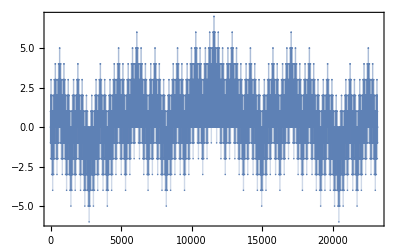

```mathematica
seq=infl["B",23];
sub1=StringPartition[seq,2];
sub1=sub1/.{"AB"->1,"BA"->-1,"AA"->0};
tbl=Table[Total [sub1[[;;i]]],{i,Length[sub1]}];
ListPlot[%,PlotRange->All,Filling->Axis]
```

The E=0 wavefunction of the hopping model is related to the quasiperiodic function f:
|ψ_(2j)| = ρ^f(j) (and on the odd sites ψ = 0)

```mathematica
(* periodic approximant (of wavevector k) of the Fibonacci chain, in normal numbering, with next-to-nearest neighbours uniform couplings *)
h[l_,ρ_,k_]:=Block[{αl,fib,jump,tbl,ar,n=Fibonacci[l],p=Fibonacci[l-1],q=Fibonacci[l],seq},
(*αl=p/q;
fib[j_]:=IntegerPart[(1+αl)^-1 (j+1)]-IntegerPart[(1+αl)^-1 j];
jump[j_]:=If[fib[j-1]<1,1.,ρ];*)
seq=infl["B",l-1];
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];
(* boundary conditions for the nearest neighbour hoppings *)
(*PrependTo[tbl,{1,n}->Exp[I k]jump[n]];*)

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(*pass to conumbering*)
co[l_,j_]:=Mod[Fibonacci[l-2] j,Fibonacci[l]]
toco[l_,list_]:=Block[{perm},
perm=co[l,#]&/@Range[Fibonacci[l]];
list[[perm]]]
```

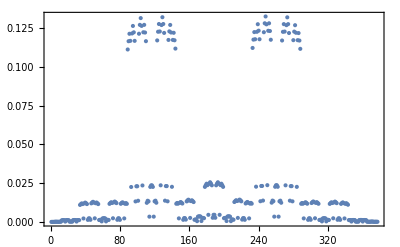

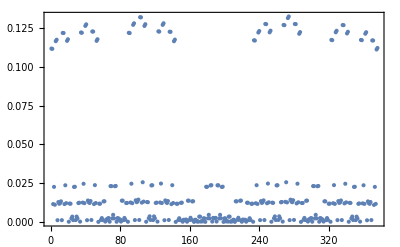

```mathematica
l=14;
{sp,wf}=Eigensystem[h[l,0.1,0]];
ord=Ordering[sp];
sp=sp[[ord]];
wf=wf[[ord]];
ListPlot[Abs[wf[[-1]]]]
ListPlot[toco[l,Abs[wf[[1]]]]]
```

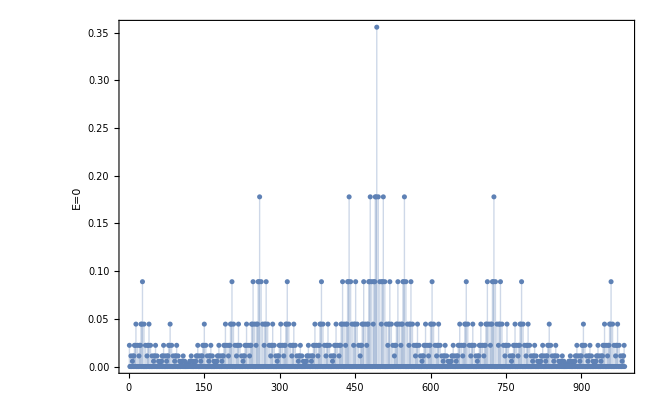

```mathematica
k=4;
l=16;
L=Fibonacci[l];
ρ=0.5;
{spec,wf}=Eigensystem[h[l,ρ,0.]];
ordering=Ordering[spec];
spec=spec[[ordering]];
wf=wf[[ordering]];
a=(L+1)/2;
ListPlot[Abs[wf[[a]]],PlotRange->All,Filling->Axis,FrameLabel->"E="<>ToString[Chop[spec[[a]]]]];
ListPlot[toco[l,Abs[wf[[a]]]],PlotRange->All,Filling->Axis,FrameLabel->"E="<>ToString[Chop[spec[[a]]]]]
```

```mathematica
342-145
```

197

```mathematica
Fibonacci/@Range[5,15]
```

{5,8,13,21,34,55,89,144,233,377,610}

```mathematica
wf[[a]]//Chop;
nonzero=%[[;;;;2]];
m=Abs@nonzero[[1]];
nonzero/=m;
Log[Abs@nonzero]/Log[ρ]//Round
```

{0,1,1,0,-1,0,0,-1,-2,-1,0,0,-1,0,1,1,0,1,2,2,1,0,1,1,0,-1,0,1}

```mathematica
tbl1
```

{0,1,1,0,-1,0,0,-1,-2,-1,0,0,-1,0,1,1,0,1,2,2,1,0,1,1,0,-1,0,1,1,0,1,2,2,1,2,3,3,2,1,2,2,1,0,1,1,0,-1,0,1,1,0,1,2,2,1,0,1,1,0,-1,0,0,-1,-2,-1,0,0,-1,0,1,1,0,-1,0,0,-1,-2,-1,-1,-2,-3,-2,-1,-1,-2,-1,0,0,-1,0,1,1,0,-1,0,0,-1,-2,-1,0,0,-1,0,1,1,0,1,2,2,1,0,1,1,0,-1,0,0,-1,-2,-1,0,0,-1,0,1,1,0,-1,0,0,-1,-2,-1,-1,-2,-3,-2,-1,-1,-2,-1,0,0,-1,-2,-1,-1,-2,-3,-2,-2,-3,-4,-3,-2,-2,-3,-2,-1,-1,-2,-1,0,0,-1,-2,-1,-1,-2,-3,-2,-1,-1,-2,-1,0,0,-1,0,1,1,0,-1,0,0,-1,-2,-1,0}

987

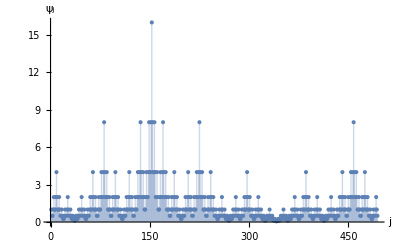

```mathematica
ρ=0.5;
seq=infl["B",15];
StringLength[seq]
sub1=StringPartition[seq,2];
sub1=sub1/.{"AB"->1,"BA"->-1,"AA"->0};
tbl1=Table[Plus@@(sub1[[;;i]]),{i,0,Length[sub1]}];
ListPlot[ρ^tbl1,PlotRange->All,Filling->Axis,AxesLabel->stylize/@{"j","ψ_j"},PlotStyle->{st,BostonBlue}]
```

```mathematica
Export[NotebookDirectory[]<>"wavefunction.pdf",%]
```

/home/nicolas/git/talks/SinJe LPT 2016/img/wavefunction.pdf

```mathematica
tbl1
%//Sort
Counts[%]
```

{0,1,1,0,-1,0,0,-1,-2,-1,0,0,-1,0,1,1,0,1,2,2,1,0,1,1,0,-1,0,1,1,0,1,2,2,1,2,3,3,2,1,2,2,1,0,1,1,0,-1,0,1,1,0,1,2,2,1,0,1,1,0,-1,0,0,-1,-2,-1,0,0,-1,0,1,1,0,-1}

{-2,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,3,3}

<|-2→2,-1→11,0→24,1→24,2→10,3→2|>

```mathematica
Fibonacci/@Range[2,10]
```

{1,2,3,5,8,13,21,34,55}

```mathematica
seq=infl["B",7];
sub2=StringReplace[StringPartition[seq,2],{"AB"->"A","BA"->"A","AA"->"B"}]
```

{A,B,A,A,A,B,A,A,A,A}

```mathematica
Fibonacci[15]
```

610

```mathematica
Fibonacci[16]
```

987

```mathematica
seq
```

ABAABABAABAABABAABABA